## Definiciones

```mathematica
SetDirectory[NotebookDirectory[]];Get["BilliardsDTQW.wl"];
Get["/home/jadeleon/Documents/chaos_meets_channels/Mathematica_packages/QMB.wl"]
```

## Distribución de probabilidad

```mathematica
xc=75.;

(* Construir la base del espacio total *)
basis=Basis[xc];reversedBasis=Reverse[basis];
tags=Tag/@basis;

(* Construir shifts *)
ShiftX=HorizontalShift[xc,tags,reversedBasis];
ShiftY=VerticalShift[xc,tags];
```

```mathematica
(* Construir las monedas *)
α=Pi/4.;
C1=C2=Chop[KroneckerProduct[IdentityMatrix[Round[DimH[xc]]/2, SparseArray], 
  SparseArray[N[{{Cos[α],Sin[α]},{-Exp[I*Pi/4.]*Sin[α],Exp[I*Pi/4.]*Cos[α]}}]]]];

(* Construir el operador unitario de un paso de la DTQW *)
U=ShiftX.C2.ShiftY.C1;
```

```mathematica
(* Construir la base del espacio de posición *)
pos=Flatten[Table[{x,y},{x,0,2*xc},{y,0,VerticalBoundary[x,xc]}],1];
```

```mathematica
(* Encontrar alguna posición deseada *)
{x,y}={75,37};
xyPos=Position[pos,z_/;z=={x,y}][[1,1]]
```

5738

```mathematica
tmax=209;c0={1/√2.,I/√2.}(* estado inicial moneda *);
probs={};
ψ=Join[ConstantArray[0,xyPos],c0,ConstantArray[0,2*Length[pos]-2-xyPos]];AppendTo[probs,Total[Abs[ψ[[#;;#+1]]]^2]&/@Range[1,2*Length[pos]-1,2]];
AbsoluteTiming[
Do[ψ=Chop[U.ψ];AppendTo[probs,Total[Abs[ψ[[#;;#+1]]]^2]&/@Range[1,2*Length[pos]-1,2]];
,tmax]
]
```

{13.381,Null}

```mathematica
(* Construir {x,y,0.} para los (x,y) que no están dentro del estadio *)
r=Join[#,{0.}]&/@Complement[Flatten[Table[{x,y},{x,0,2*xc},{y,0,xc}],1],pos];
```

```mathematica
frames=Table[
ListDensityPlot[Join[Join@@@Transpose[Join[{pos},{Transpose[{probs[[t]]}]}]],r],
InterpolationOrder->0,
ColorFunction->"BlueGreenYellow",
PlotRange->{Automatic,Automatic,Full},
PlotLabel->Style["ψ_0=75,370_y, t = "<>ToString[t-1],Black,FontSize->20],
(*PlotLegends->Placed[BarLegend[{Automatic,{0,Max[i]}},LabelStyle->Directive[FontFamily->"Arial",FontSize->20,Black]],Automatic],*)
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->20,Black],
AspectRatio->1/2,
ImageSize->500
]
,{t,tmax+1}];
```

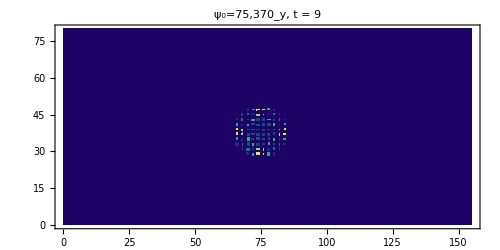

```mathematica
frames[[10]]
```

Exportar frames:

```mathematica
(*Crear carpeta para los frames*)
If[!DirectoryQ["frames"],CreateDirectory["frames"]];

(*Exportar los cuadros*)
Do[Export[FileNameJoin[{"frames",StringPadLeft[ToString[i],4,"0"]<>".png"}],frames[[i]]],{i,Length[frames]}]
```